```mathematica
elcdm[z_]=√(om (1+z)^3+1-om)
```

√(1-om+om (1+z)^3)

```mathematica
elinear[z_] = Sqrt[om(1+z)^3 + (1- om)(1+z)^(3(1+w0linear - w1linear)) Exp[3 w1linear z]]
```

√(om (1+z)^3+ⅇ^(3 w1linear z) (1-om) (1+z)^(3 (1+w0linear-w1linear)))

```mathematica
elinder[z_] = Sqrt[om(1+z)^3 + (1-om)(1+z)^(3(1 + w0linder + w1linder))Exp[3 w1linder (1/(1+z) - 1)]]
```

√(om (1+z)^3+ⅇ^(3 w1linder (-1+1/(1+z))) (1-om) (1+z)^(3 (1+w0linder+w1linder)))

```mathematica
eode[z_] = Sqrt[om (1+z)^3 + a1 Cos[a2 z^2 + a3] + (1 - a1 Cos[a3] - om)]
```

√(1-om+om (1+z)^3-a1 Cos[a3]+a1 Cos[a3+a2 z^2])

```mathematica
q[z_, e_]:= -1 + (1+z)e'[z]/e[z]
```

```mathematica
qLCDM= q[z, elcdm]
```

-1+(3 om (1+z)^3)/(2 (1-om+om (1+z)^3))

```mathematica
qLinear = q[z, elinear]
```

-1+((1+z) (3 om (1+z)^2+3 ⅇ^(3 w1linear z) (1-om) (1+w0linear-w1linear) (1+z)^(-1+3 (1+w0linear-w1linear))+3 ⅇ^(3 w1linear z) (1-om) w1linear (1+z)^(3 (1+w0linear-w1linear))))/(2 (om (1+z)^3+ⅇ^(3 w1linear z) (1-om) (1+z)^(3 (1+w0linear-w1linear))))

```mathematica
qLinder = q[z, elinder]
```

-1+((1+z) (3 om (1+z)^2-3 ⅇ^(3 w1linder (-1+1/(1+z))) (1-om) w1linder (1+z)^(-2+3 (1+w0linder+w1linder))+3 ⅇ^(3 w1linder (-1+1/(1+z))) (1-om) (1+w0linder+w1linder) (1+z)^(-1+3 (1+w0linder+w1linder))))/(2 (om (1+z)^3+ⅇ^(3 w1linder (-1+1/(1+z))) (1-om) (1+z)^(3 (1+w0linder+w1linder))))

```mathematica
qOA = q[z, eode]
```

-1+((1+z) (3 om (1+z)^2-2 a1 a2 z Sin[a3+a2 z^2]))/(2 (1-om+om (1+z)^3-a1 Cos[a3]+a1 Cos[a3+a2 z^2]))

```mathematica
om = 0.3;
w0linear = -1.25;
w1linear = 1.97;
w0linder=-1.29;
w1linder= 2.84;
a1 = -3.36;
a2= 2.12;
a3 = -0.06 Pi;
```

```mathematica
ploteLCDM = Plot[elcdm[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"LCDM"];
```

```mathematica
ploteLinear = Plot[elinear[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"Linear"];
```

```mathematica
ploteLinder = Plot[elinder[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"Linder"];
```

```mathematica
ploteOA = Plot[eode[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"OA"];
```

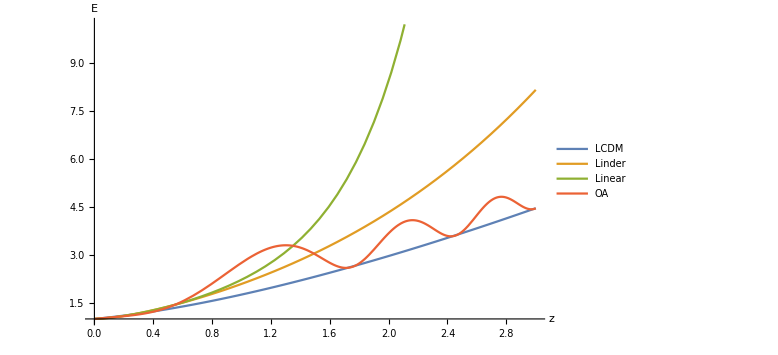

```mathematica
Plot[{elcdm[z], elinder[z], elinear[z], eode[z]}, {z, 0, 3}, PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["E", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

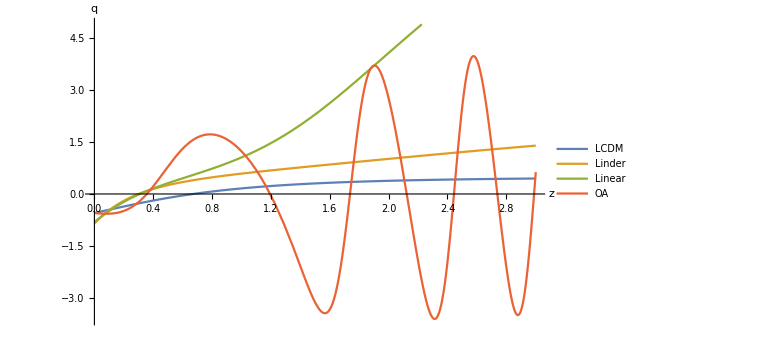

```mathematica
Plot[{q[z, elcdm], q[z,elinder], q[z,elinear], q[z,eode]}, {z, 0, 3}, PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["q", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

```mathematica
r[z_, e_]= q[z,e] (2 q[z,e] + 1) + (1+z)D[q[z,e],z]
```

(-1+((1+z) e'[z])/e[z]) (1+2 (-1+((1+z) e'[z])/e[z]))+(1+z) (e'[z]/e[z]-((1+z) e'[z]^2)/e[z]^2+((1+z) e''[z])/e[z])

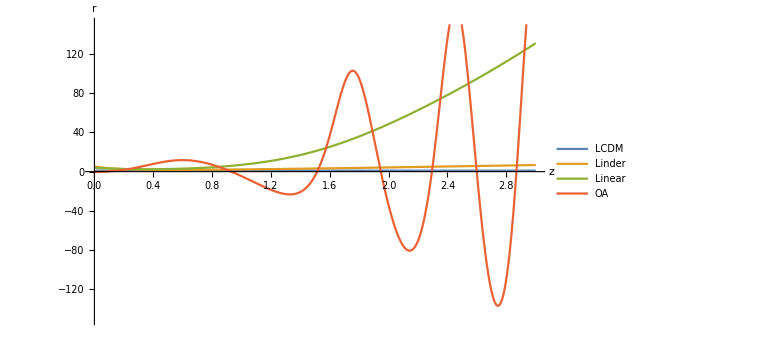

```mathematica
Plot[{r[z, elcdm], r[z,elinder], r[z,elinear], r[z,eode]}, {z, 0, 3}, PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["r", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large, PlotRange->{-150,150}]
```

```mathematica
s[z_, e_] = (r[z,e] - 1) / (3 ((q[z, e]) - 1/2))
```

(-1+(-1+((1+z) e'[z])/e[z]) (1+2 (-1+((1+z) e'[z])/e[z]))+(1+z) (e'[z]/e[z]-((1+z) e'[z]^2)/e[z]^2+((1+z) e''[z])/e[z]))/(3 (-3/2+((1+z) e'[z])/e[z]))

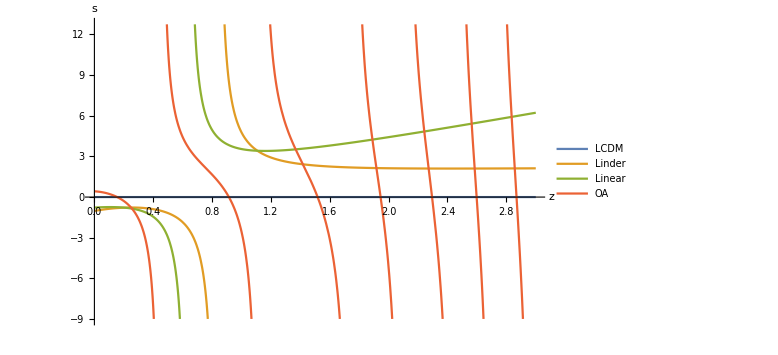

```mathematica
Plot[{s[z, elcdm], s[z,elinder], s[z,elinear], s[z,eode]}, {z, 0, 3}, PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["s", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

```mathematica
elcdmA[a_]=√(om/a^3+1-om)
```

√(0.7+0.3/a^3)

```mathematica
s = NDSolve[{d''[a] + (3/a + elcdmA'[a]/elcdmA[a])d'[a] - 3/2 om / (a^5 elcdmA[a]^2) d[a] == 0, d[0.01]== 0.001, d'[0.01]==0.01}, d, {a, 0.001, 1}]
```

{{d→InterpolatingFunction[…]}}

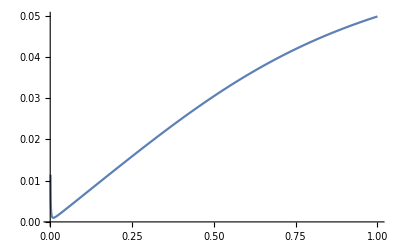

```mathematica
Plot[d[a]/. s, {a, 0.001, 1}]
```

```mathematica
f[a_] := (d'[a] /. s) / (d[a] /. s) * (a)
```

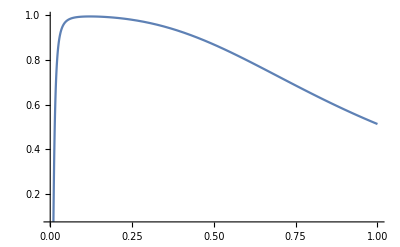

```mathematica
Plot[f[a], {a, 0.001, 1}]
```